100000

200

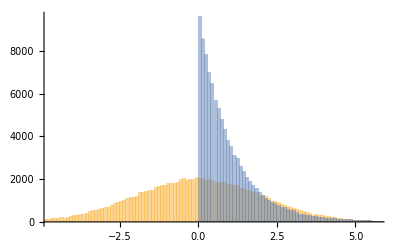

8.72935

```mathematica
Clear["Global`*"]
n = 100000
bins = 200

datExp = RandomVariate[NormalDistribution[0,2],n];
datExp2 = RandomVariate[ExponentialDistribution[1],n]
ListPlot[datExp];
Histogram[{datExp,datExp2}, bins]
Kurtosis[datExp2]
```

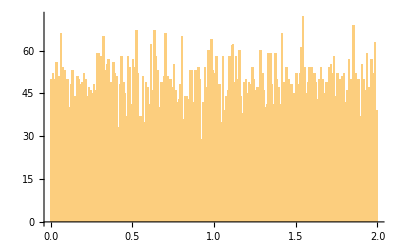

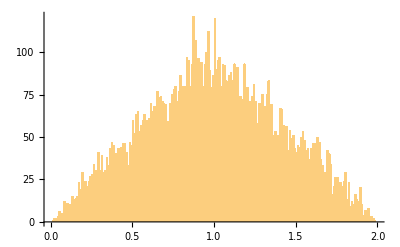

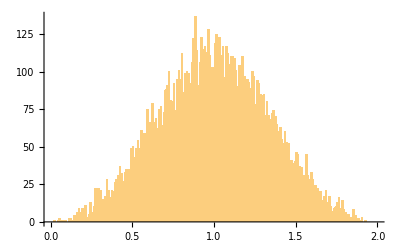

i =

1

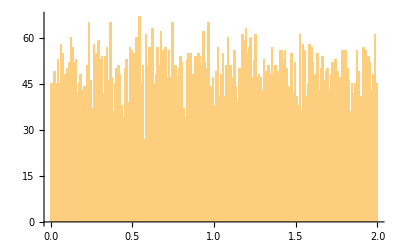

i =

2

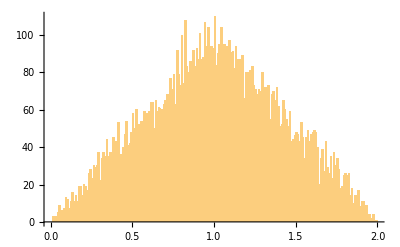

i =

3

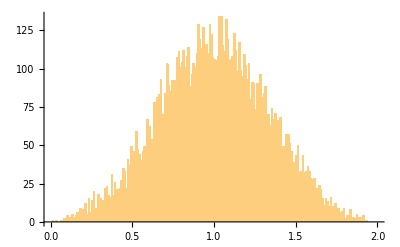

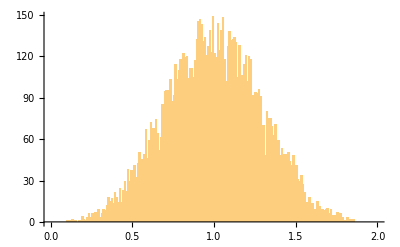

```mathematica
For[ i = 1 , i <= 3, i++, 
avgs = {};
For[j=1,j <= 10000, j++,
AppendTo[avgs,Mean[RandomReal[{0,2} , i]]]
];
Print["i = "];
Print[i];
Print[Histogram[avgs,{0,2,0.01}]]
]
```

{0.123}

Sin[π x]

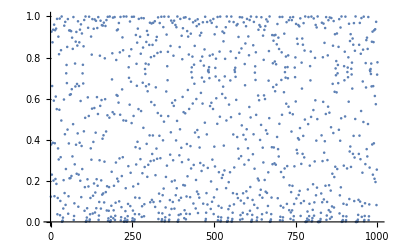

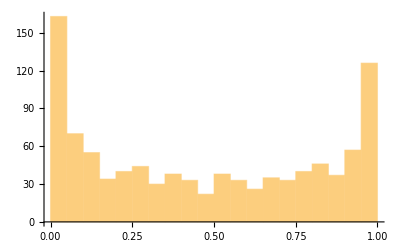

```mathematica
Clear["Global`*"]
P = {0.123}
model[x_] = Sin[π x]
For[i=2,i<=1000,i++,AppendTo[P,model[P[[i-1]]]]];
ListPlot[P]
Histogram[P,20]
```

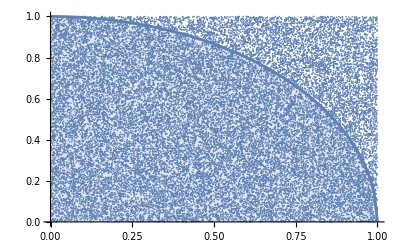

3.15197

```mathematica
Clear["Global`*"]
pltCircle = ListLinePlot[Table[{x,Sqrt[1-x^2]} , {x,0,1,0.01}], Filling->Bottom];
pts = {};
a = 0;
b = 0;
For[i = 1 , i<30000, i++ ,

x = RandomReal[{0,1}];
y = RandomReal[{0,1}];
b = b + 1;
If[x^2 + y^2 <= 1, a = a + 1;];
AppendTo[pts,{x,y}];
]
pltPoints = ListPlot[pts];
Show[{pltPoints , pltCircle}]
4 a / b // N
```

```mathematica
Clear["Global`*"]
f[x_] =Exp[-3 x ] Cos[x]/(1+Sinh[2*x]*(Log[x])^2)
a = 1;
b = 3;
n = 2000;
avgs = {};
For[i=1, i <= 1000, i ++ ,
sum = 0;
For[j = 1, j <= n, j++,
sum = sum + (b-a) * f[RandomReal[{a,b}]]/ n
];
AppendTo[avgs, sum]
]
```

(ⅇ^(-3 x) Cos[x])/(1+Log[x]^2 Sinh[2 x])

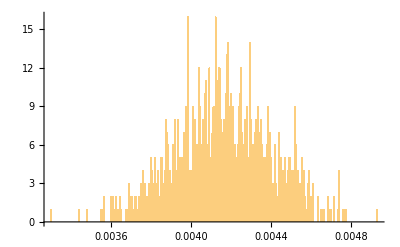

```mathematica
Histogram[avgs, 400]
```

```mathematica
NIntegrate[f[x] , {x,a,b}]
```

0.00415512

```mathematica
HistogramList[avgs, 400 ][[1]][[200]] // N
```

0.004295

```mathematica
Clear["Global`*"]
f[x_, y_] = Log[1 + x^2 + y^2] Exp[π/(1 + x)] Sin[y]
a = 2;
b = π;
n = 2000;
avgs = {}
For[i=1, i <= 1000, i ++ ,
sum = 0;
For[j = 1, j <= n, j++,
sum = sum + (b-a)^2 * f[RandomReal[{a,b}] , RandomReal[{a,b}]]/ n
];
AppendTo[avgs, sum]]
```

ⅇ^(π/(1+x)) Log[1+x^2+y^2] Sin[y]

{}

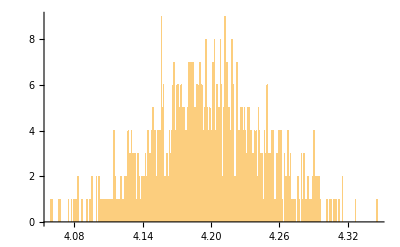

```mathematica
Histogram[avgs, 400]
```

```mathematica
NIntegrate[f[x,y] , {x,a,b},{y,a,b}]
h = HistogramList[avgs, 40 ];
h[[1]][[Flatten[Position[h[[2]],Max[h[[2]]]]][[1]]]] // N
```

4.195

4.18